# 1loop integral (EDM)

```mathematica
gloop[z_]:=NIntegrate[1/(x(1-x)-z)Log[x(1-x)/z],{x,0,1}]
```

```mathematica
gloop[173^2/125^2]
```

1.50051

# Thermal masses in xSM

```mathematica
mh2=-μ^2+3h^2 λ+λhs s^2;ms2=μs^2+3λs s^2+λhs h^2;(*From 1409.0005 *)
```

```mathematica
Vthermal[m_]:=ExpandAll[T^4 (1/24(m/T)^2 - 1/(12 π) (m/T)^(3)+1/2/(4π)^2 3/4(m/T)^4)](*from 2008.09136 *)
```

```mathematica
Vthermal[√mh2]
```

1/8 h^2 T^2 λ+(27 h^4 λ^2)/(128 π^2)+1/24 s^2 T^2 λhs+(9 h^2 s^2 λ λhs)/(64 π^2)+(3 s^4 λhs^2)/(128 π^2)-(T^2 μ^2)/24-(9 h^2 λ μ^2)/(64 π^2)-(3 s^2 λhs μ^2)/(64 π^2)+(3 μ^4)/(128 π^2)-(h^2 T λ √(3 h^2 λ+s^2 λhs-μ^2))/(4 π)-(s^2 T λhs √(3 h^2 λ+s^2 λhs-μ^2))/(12 π)+(T μ^2 √(3 h^2 λ+s^2 λhs-μ^2))/(12 π)

```mathematica
Expand[2Coefficient[Vthermal[√mh2]+Vthermal[√ms2],h^2 T^2]]
```

λ/4+λhs/12

```mathematica
Expand[2Coefficient[Vthermal[√mh2]+Vthermal[√ms2],s^2 T^2]]
```

λhs/12+λs/4

# Potential barrier in xSM (high T approx)

```mathematica
ClearAll["Global`*"];
Clear[Φ,h,S,mh,mus,μh,μ2,λ,λ2,λmix,v,Q,g,g1,δλ,δλmix,δμ2,DV0,MinimaConditions,MassMatrix];
Φc={ϕp,ϕ1-I ϕ2};Φ={ϕm,ϕ1+I ϕ2};
V0[Gp_,Gm_,G0_,h_,s_]:=ComplexExpand[-μh Φc.Φ+ μs/2 S^2+λ(Φc.Φ)^2+λs S^4/4+λhs S^2/2 Φc.Φ]/.{ϕp->Gp,ϕm->Gm,ϕ1->h/√2,ϕ2->G0/√2,S->s};
DV0[i_]:=D[V0[Gp,Gm,G0,h,s],{h,s,Gp,Gm,G0}[[i]]];MinimaConditions=Expand[Table[DV0[i],{i,1,5}]/.{Gp->0,Gm->0,G0->0,h->v,s->0}];MassMatrix[i_,j_]:=D[V0[Gp,Gm,G0,h,s],{h,s,Gp,Gm,G0}[[i]],{h,s,Gp,Gm,G0}[[j]]]/.{Gp->0,Gm->0,G0->0};
```

```mathematica
Clear[λ,μs,μh];λ=λ/.Solve[MinimaConditions[[1]]==0,λ][[1]];μs=ms^2-v^2λhs/2;μh=mh^2/2;
```

```mathematica
MinimaConditions
```

{0,0,0,0,0}

```mathematica
MatrixForm[Table[MassMatrix[i,j],{i,1,2},{j,1,2}]]/.{h->h,s->s}
```

(3 h^2 λ+(s^2 λhs)/2-μh | h s λhs
h s λhs | (h^2 λhs)/2+3 s^2 λs+μs)

```mathematica
Vthermal[m_]:=ExpandAll[T^4 (1/24(m/T)^2 - 1/(12 π) (m/T)^(3)+1/2/(4π)^2 3/4(m/T)^4)](*from 2008.09136 *)
```

```mathematica
{m1,m2}=Eigenvalues[Table[MassMatrix[i,j],{i,1,2},{j,1,2}]];
```

```mathematica
Simplify[{-m1+m2}/.{s->0},{mh>0,ms>0,h>0,v>0}]
```

{(√((h^2 (3 mh^2-v^2 λhs)+v^2 (-mh^2-2 ms^2+v^2 λhs))^2))/(2 v^2)}

```mathematica
Coefficient[FullSimplify[Vthermal[√(h^2(6λ+λhs))],h>0],h^3]
```

-(T √((3 mh^2)/v^2+λhs) (3 mh^2+v^2 λhs))/(12 π v^2)

# Potential

```mathematica
ClearAll["Global`*"]
```

```mathematica
Φc={ϕp,ϕ1-I ϕ2};Φ={ϕm,ϕ1+I ϕ2};
V0[Gp_,Gm_,G0_,h_,s_]:=ComplexExpand[-μh Φc.Φ+λ(Φc.Φ)^2- μs/2 S^2-μ3 S^3/3+
λs S^4/4+λmix S^2/2 Φc.Φ+μϕs (Φc.Φ) S]/.{ϕp->Gp,ϕm->Gm,ϕ1->h/√2,ϕ2->G0/√2,S->s};
DV0[i_]:=D[V0[Gp,Gm,G0,h,s],{h,s,Gp,Gm,G0}[[i]]];MinimaConditions=Expand[Table[DV0[i],{i,1,5}]/.{Gp->0,Gm->0,G0->0,h->v,s->w}];MassMatrix[i_,j_]:=D[V0[Gp,Gm,G0,h,s],{h,s,Gp,Gm,G0}[[i]],{h,s,Gp,Gm,G0}[[j]]]/.{Gp->0,Gm->0,G0->0};
```

```mathematica
FullSimplify[MatrixForm[Table[MassMatrix[i,j],{i,1,5},{j,1,5}]]]
```

(3 h^2 λ+(s^2 λmix)/2-μh+s μϕs | h (s λmix+μϕs) | 0 | 0 | 0
h (s λmix+μϕs) | (h^2 λmix)/2+3 s^2 λs-2 s μ3-μs | 0 | 0 | 0
0 | 0 | 0 | h^2 λ+(s^2 λmix)/2-μh+s μϕs | 0
0 | 0 | h^2 λ+(s^2 λmix)/2-μh+s μϕs | 0 | 0
0 | 0 | 0 | 0 | h^2 λ+(s^2 λmix)/2-μh+s μϕs)

```mathematica
V0[0,0,0,h,s]
```

(h^4 λ)/4+1/4 h^2 s^2 λmix+(s^4 λs)/4-(s^3 μ3)/3-(h^2 μh)/2-(s^2 μs)/2+1/2 h^2 s μϕs

```mathematica
MinimaConditions
```

{v^3 λ+1/2 v w^2 λmix-v μh+v w μϕs,1/2 v^2 w λmix+w^3 λs-w^2 μ3-w μs+(v^2 μϕs)/2,0,0,0}

```mathematica
Clear[μh];μh=μh/.Solve[MinimaConditions[[1]]==0,μh][[1]]
```

1/2 (2 v^2 λ+w^2 λmix+2 w μϕs)

```mathematica
Clear[μs];μs=μs/.Solve[MinimaConditions[[2]]==0,μs][[1]]
```

(v^2 w λmix+2 w^3 λs-2 w^2 μ3+v^2 μϕs)/(2 w)

```mathematica
ExpandAll[μh]
```

v^2 λ+(w^2 λmix)/2+w μϕs

```mathematica
FullSimplify[MinimaConditions]
```

{0,0,0,0,0}

```mathematica
MassMat=Table[MassMatrix[i,j],{i,1,2},{j,1,2}]/.{h->v,s->w};MatrixForm[MassMat]
```

(2 v^2 λ | v w λmix+v μϕs
v w λmix+v μϕs | 2 w^2 λs-w μ3-(v^2 μϕs)/(2 w))

```mathematica
Rotmatrix={{Cos[α],-Sin[α]},{Sin[α],Cos[α]}};MatrixForm[Rotmatrix]
```

(Cos[α] | -Sin[α]
Sin[α] | Cos[α])

```mathematica
RMRT=FullSimplify[Transpose[Rotmatrix].MassMat.Rotmatrix];MatrixForm[RMRT]
```

(2 v^2 λ Cos[α]^2+(2 w^2 λs-w μ3-(v^2 μϕs)/(2 w)) Sin[α]^2+v (w λmix+μϕs) Sin[2 α] | v (w λmix+μϕs) Cos[2 α]-((2 w^2 (-2 w λs+μ3)+v^2 (4 w λ+μϕs)) Sin[2 α])/(4 w)
v (w λmix+μϕs) Cos[2 α]-((2 w^2 (-2 w λs+μ3)+v^2 (4 w λ+μϕs)) Sin[2 α])/(4 w) | (2 w^2 λs-w μ3-(v^2 μϕs)/(2 w)) Cos[α]^2+2 v Sin[α] (-(w λmix+μϕs) Cos[α]+v λ Sin[α]))

```mathematica
Clear[λmix];λmix=λmix/.Solve[RMRT[[1,2]]==0,λmix][[1]];
```

```mathematica
Clear[λ,λs];{λ,λs}={λ,λs}/.Solve[{FullSimplify[(RMRT[[1,1]]-RMRT[[2,2]])Cos[2α]]==(mh^2-ms^2)Cos[2α],FullSimplify[RMRT[[1,1]]+RMRT[[2,2]]]==(ms^2+mh^2)},{λ,λs}][[1]]
```

{-(-mh^2-ms^2-mh^2 Cos[2 α]+ms^2 Cos[2 α])/(4 v^2),-(-mh^2 w-ms^2 w-2 w^2 μ3-v^2 μϕs+mh^2 w Cos[2 α]-ms^2 w Cos[2 α])/(4 w^3)}

```mathematica
FullSimplify[λs]
```

(w (mh^2+ms^2+2 w μ3)+v^2 μϕs+(-mh^2+ms^2) w Cos[2 α])/(4 w^3)

```mathematica
fun[hh_,ss_]:=Table[MassMatrix[i,j],{i,1,2},{j,1,2}]/.{h->hh,s->ss};
gradFun[hh_,ss_]:={D[V0[0,0,0,h,s],s],D[V0[0,0,0,h,s],h]}/.{h->hh,s->ss};
MatrixForm[fun[hh,ss]]
```

(-mh^2/4-ms^2/4+(3 hh^2 mh^2)/(4 v^2)+(3 hh^2 ms^2)/(4 v^2)+ss μϕs-(ss^2 μϕs)/(2 w)-(w μϕs)/2-1/4 mh^2 Cos[2 α]+1/4 ms^2 Cos[2 α]+(3 hh^2 mh^2 Cos[2 α])/(4 v^2)-(3 hh^2 ms^2 Cos[2 α])/(4 v^2)+(mh^2 ss^2 Cos[2 α] Sin[4 α])/(4 v w (1+Cos[4 α]))-(ms^2 ss^2 Cos[2 α] Sin[4 α])/(4 v w (1+Cos[4 α]))-(mh^2 w Cos[2 α] Sin[4 α])/(4 v (1+Cos[4 α]))+(ms^2 w Cos[2 α] Sin[4 α])/(4 v (1+Cos[4 α])) | hh μϕs-(hh ss μϕs)/w+(hh mh^2 ss Cos[2 α] Sin[4 α])/(2 v w (1+Cos[4 α]))-(hh ms^2 ss Cos[2 α] Sin[4 α])/(2 v w (1+Cos[4 α]))
hh μϕs-(hh ss μϕs)/w+(hh mh^2 ss Cos[2 α] Sin[4 α])/(2 v w (1+Cos[4 α]))-(hh ms^2 ss Cos[2 α] Sin[4 α])/(2 v w (1+Cos[4 α])) | -mh^2/4-ms^2/4+(3 mh^2 ss^2)/(4 w^2)+(3 ms^2 ss^2)/(4 w^2)-2 ss μ3+(3 ss^2 μ3)/(2 w)+(w μ3)/2+(3 ss^2 v^2 μϕs)/(4 w^3)-(hh^2 μϕs)/(2 w)-(v^2 μϕs)/(4 w)+1/4 mh^2 Cos[2 α]-1/4 ms^2 Cos[2 α]-(3 mh^2 ss^2 Cos[2 α])/(4 w^2)+(3 ms^2 ss^2 Cos[2 α])/(4 w^2)+(hh^2 mh^2 Cos[2 α] Sin[4 α])/(4 v w (1+Cos[4 α]))-(hh^2 ms^2 Cos[2 α] Sin[4 α])/(4 v w (1+Cos[4 α]))-(mh^2 v Cos[2 α] Sin[4 α])/(4 w (1+Cos[4 α]))+(ms^2 v Cos[2 α] Sin[4 α])/(4 w (1+Cos[4 α])))

```mathematica
Clear[μ3,μϕs];μ3=0;μϕs=0;
```

```mathematica
Simplify[TrigFactor[λs]]
```

(ms^2 Cos[α]^2+mh^2 Sin[α]^2)/(2 w^2)

```mathematica
FullSimplify[TrigFactor[λ]]
```

(mh^2 Cos[α]^2+ms^2 Sin[α]^2)/(2 v^2)

```mathematica
FullSimplify[TrigExpand[λmix]]
```

((mh-ms) (mh+ms) Cos[α] Sin[α])/(v w)

```mathematica
Simplify[TrigExpand[μh]]
```

((mh^2+ms^2) v+(mh^2-ms^2) v Cos[2 α]+(mh^2-ms^2) w Sin[2 α])/(4 v)

```mathematica
Simplify[TrigExpand[μs]]
```

((mh^2+ms^2) w-(mh^2-ms^2) w Cos[2 α]+(mh^2-ms^2) v Sin[2 α])/(4 w)

```mathematica
FullSimplify[4 μh ]
```

mh^2+ms^2+((mh-ms) (mh+ms) (v Cos[2 α]+w Sin[2 α]))/v

```mathematica
Reduce[λs<4 π,{ms},ms∈Reals]
```

Reduce[-(-mh^2 w-ms^2 w+mh^2 w Cos[2 α]-ms^2 w Cos[2 α])/(4 w^3)<4 π,{ms},ms∈ℝ]

```mathematica
Reduce[μh==0&&μs==0&&λs<4 π&&λ<4 π&&Abs[λmix]<4 π,{ms,w},Reals]
```

$Aborted

# Potential 2nd parametrization

```mathematica
ClearAll["Global`*"]
```

```mathematica
Φc={ϕp,ϕ1-I ϕ2};Φ={ϕm,ϕ1+I ϕ2};
V0[Gp_,Gm_,G0_,h_,s_]:=ComplexExpand[-μh Φc.Φ+λ(Φc.Φ)^2- μs/2 S^2-μ3 S^3/3+
λs S^4/4+λmix S^2/2 Φc.Φ+μϕs (Φc.Φ) S]/.{ϕp->Gp,ϕm->Gm,ϕ1->h/√2,ϕ2->G0/√2,S->s};
DV0[i_]:=D[V0[Gp,Gm,G0,h,s],{h,s,Gp,Gm,G0}[[i]]];MinimaConditions=Expand[Table[DV0[i],{i,1,5}]/.{Gp->0,Gm->0,G0->0,h->v,s->w}];MassMatrix[i_,j_]:=D[V0[Gp,Gm,G0,h,s],{h,s,Gp,Gm,G0}[[i]],{h,s,Gp,Gm,G0}[[j]]]/.{Gp->0,Gm->0,G0->0};
```

```mathematica
FullSimplify[MatrixForm[Table[MassMatrix[i,j],{i,1,5},{j,1,5}]]]
```

(3 h^2 λ+(s^2 λmix)/2-μh+s μϕs | h (s λmix+μϕs) | 0 | 0 | 0
h (s λmix+μϕs) | (h^2 λmix)/2+3 s^2 λs-2 s μ3-μs | 0 | 0 | 0
0 | 0 | 0 | h^2 λ+(s^2 λmix)/2-μh+s μϕs | 0
0 | 0 | h^2 λ+(s^2 λmix)/2-μh+s μϕs | 0 | 0
0 | 0 | 0 | 0 | h^2 λ+(s^2 λmix)/2-μh+s μϕs)

```mathematica
V0[0,0,0,h,s]
```

(h^4 λ)/4+1/4 h^2 s^2 λmix+(s^4 λs)/4-(s^3 μ3)/3-(h^2 μh)/2-(s^2 μs)/2+1/2 h^2 s μϕs

```mathematica
MinimaConditions
```

{v^3 λ+1/2 v w^2 λmix-v μh+v w μϕs,1/2 v^2 w λmix+w^3 λs-w^2 μ3-w μs+(v^2 μϕs)/2,0,0,0}

```mathematica
Clear[μh];μh=μh/.Solve[MinimaConditions[[1]]==0,μh][[1]]
```

1/2 (2 v^2 λ+w^2 λmix+2 w μϕs)

```mathematica
Clear[μs];μs=μs/.Solve[MinimaConditions[[2]]==0,μs][[1]]
```

(v^2 w λmix+2 w^3 λs-2 w^2 μ3+v^2 μϕs)/(2 w)

```mathematica
ExpandAll[μh]
```

v^2 λ+(w^2 λmix)/2+w μϕs

```mathematica
FullSimplify[MinimaConditions]
```

{0,0,0,0,0}

```mathematica
MassMat=Table[MassMatrix[i,j],{i,1,2},{j,1,2}]/.{h->v,s->w};MatrixForm[MassMat]
```

(2 v^2 λ | v w λmix+v μϕs
v w λmix+v μϕs | 2 w^2 λs-w μ3-(v^2 μϕs)/(2 w))

```mathematica
Rotmatrix={{Cos[α],-Sin[α]},{Sin[α],Cos[α]}};MatrixForm[Rotmatrix]
```

(Cos[α] | -Sin[α]
Sin[α] | Cos[α])

```mathematica
RMRT=FullSimplify[Transpose[Rotmatrix].MassMat.Rotmatrix];MatrixForm[RMRT]
```

(2 v^2 λ Cos[α]^2+(2 w^2 λs-w μ3-(v^2 μϕs)/(2 w)) Sin[α]^2+v (w λmix+μϕs) Sin[2 α] | v (w λmix+μϕs) Cos[2 α]-((2 w^2 (-2 w λs+μ3)+v^2 (4 w λ+μϕs)) Sin[2 α])/(4 w)
v (w λmix+μϕs) Cos[2 α]-((2 w^2 (-2 w λs+μ3)+v^2 (4 w λ+μϕs)) Sin[2 α])/(4 w) | (2 w^2 λs-w μ3-(v^2 μϕs)/(2 w)) Cos[α]^2+2 v Sin[α] (-(w λmix+μϕs) Cos[α]+v λ Sin[α]))

```mathematica
Clear[α];α=1/2 ArcTan[θ];
```

```mathematica
Clear[θ];θ=θ/.Solve[FullSimplify[RMRT[[1,2]]/Cos[2α]]==0,θ][[1]];
```

```mathematica
θ
```

(4 v w (w λmix+μϕs))/(4 v^2 w λ-4 w^3 λs+2 w^2 μ3+v^2 μϕs)

```mathematica
Clear[μ3]
```

```mathematica
Tr[MassMat]
```

2 v^2 λ+2 w^2 λs-w μ3-(v^2 μϕs)/(2 w)

```mathematica
Det[MassMat]
```

-v^2 w^2 λmix^2+4 v^2 w^2 λ λs-2 v^2 w λ μ3-(v^4 λ μϕs)/w-2 v^2 w λmix μϕs-v^2 μϕs^2

```mathematica
Clear[μϕs,μ3];{μϕs,μ3}={μϕs,μ3}/.FullSimplify[Solve[{Tr[MassMat]==2 mh^2,Det[MassMat]==mh^4},{μϕs,μ3}]][[1]]
```

{-(√(-(mh^2 v-2 v^3 λ)^2)+v^2 w λmix)/v^2,(-4 mh^2 w+√(-v^2 (mh^2-2 v^2 λ)^2)+v^2 w (4 λ+λmix)+4 w^3 λs)/(2 w^2)}

```mathematica
λ=mh^2/2/v^2;
```

```mathematica
FullSimplify[μ3]
```

(-2 mh^2+v^2 λmix+4 w^2 λs)/(2 w)

```mathematica
FullSimplify[μϕs]
```

-w λmix

```mathematica
FullSimplify[θ]
```

0

```mathematica
FullSimplify[μs]
```

mh^2-(v^2 λmix)/2-w^2 λs

# Potential + Thermal corrections

```mathematica
ClearAll["Global`*"]
```

```mathematica
Φc={ϕp,ϕ1-I ϕ2};Φ={ϕm,ϕ1+I ϕ2};
V0[Gp_,Gm_,G0_,h_,s_]:=ComplexExpand[-μh Φc.Φ+λ(Φc.Φ)^2- μs/2 S^2-μ3 S^3/3+
λs S^4/4+λmix S^2/2 Φc.Φ+μϕs (Φc.Φ) S]/.{ϕp->Gp,ϕm->Gm,ϕ1->h/√2,ϕ2->G0/√2,S->s};
DV0[i_]:=D[V0[Gp,Gm,G0,h,s],{h,s,Gp,Gm,G0}[[i]]];MinimaConditions=Expand[Table[DV0[i],{i,1,5}]/.{Gp->0,Gm->0,G0->0,h->v,s->w}];MassMatrix[i_,j_]:=D[V0[Gp,Gm,G0,h,s],{h,s,Gp,Gm,G0}[[i]],{h,s,Gp,Gm,G0}[[j]]]/.{Gp->0,Gm->0,G0->0};
```

```mathematica
FullSimplify[MatrixForm[Table[MassMatrix[i,j],{i,1,5},{j,1,5}]]]
```

(3 h^2 λ+(s^2 λmix)/2-μh+s μϕs | h (s λmix+μϕs) | 0 | 0 | 0
h (s λmix+μϕs) | (h^2 λmix)/2+3 s^2 λs-2 s μ3-μs | 0 | 0 | 0
0 | 0 | 0 | h^2 λ+(s^2 λmix)/2-μh+s μϕs | 0
0 | 0 | h^2 λ+(s^2 λmix)/2-μh+s μϕs | 0 | 0
0 | 0 | 0 | 0 | h^2 λ+(s^2 λmix)/2-μh+s μϕs)

```mathematica
V0[0,0,0,h,s]
```

(h^4 λ)/4+1/4 h^2 s^2 λmix+(s^4 λs)/4-(s^3 μ3)/3-(h^2 μh)/2-(s^2 μs)/2+1/2 h^2 s μϕs

```mathematica
MinimaConditions
```

{v^3 λ+1/2 v w^2 λmix-v μh+v w μϕs,1/2 v^2 w λmix+w^3 λs-w^2 μ3-w μs+(v^2 μϕs)/2,0,0,0}

```mathematica
Clear[μh];μh=μh/.Solve[MinimaConditions[[1]]==0,μh][[1]]
```

1/2 (2 v^2 λ+w^2 λmix+2 w μϕs)

```mathematica
Clear[μs];μs=μs/.Solve[MinimaConditions[[2]]==0,μs][[1]]
```

(v^2 w λmix+2 w^3 λs-2 w^2 μ3+v^2 μϕs)/(2 w)

```mathematica
ExpandAll[μs]
```

(v^2 λmix)/2+w^2 λs-w μ3+(v^2 μϕs)/(2 w)

```mathematica
FullSimplify[MinimaConditions]
```

{0,0,0,0,0}

```mathematica
MassMat=Table[MassMatrix[i,j],{i,1,2},{j,1,2}]/.{h->v,s->w};MatrixForm[MassMat]
```

(2 v^2 λ | v w λmix+v μϕs
v w λmix+v μϕs | 2 w^2 λs-w μ3-(v^2 μϕs)/(2 w))

```mathematica
Rotmatrix={{Cos[α],-Sin[α]},{Sin[α],Cos[α]}};MatrixForm[Rotmatrix]
```

(Cos[α] | -Sin[α]
Sin[α] | Cos[α])

```mathematica
RMRT=FullSimplify[Transpose[Rotmatrix].MassMat.Rotmatrix];MatrixForm[RMRT]
```

(2 v^2 λ Cos[α]^2+(2 w^2 λs-w μ3-(v^2 μϕs)/(2 w)) Sin[α]^2+v (w λmix+μϕs) Sin[2 α] | v (w λmix+μϕs) Cos[2 α]-((2 w^2 (-2 w λs+μ3)+v^2 (4 w λ+μϕs)) Sin[2 α])/(4 w)
v (w λmix+μϕs) Cos[2 α]-((2 w^2 (-2 w λs+μ3)+v^2 (4 w λ+μϕs)) Sin[2 α])/(4 w) | (2 w^2 λs-w μ3-(v^2 μϕs)/(2 w)) Cos[α]^2+2 v Sin[α] (-(w λmix+μϕs) Cos[α]+v λ Sin[α]))

```mathematica
Clear[λmix];λmix=λmix/.Solve[RMRT[[1,2]]==0,λmix][[1]];
```

```mathematica
Clear[λ,λs];{λ,λs}={λ,λs}/.Solve[{FullSimplify[(RMRT[[1,1]]-RMRT[[2,2]])Cos[2α]]==(mh^2-ms^2)Cos[2α],FullSimplify[RMRT[[1,1]]+RMRT[[2,2]]]==(ms^2+mh^2)},{λ,λs}][[1]]
```

{-(-mh^2-ms^2-mh^2 Cos[2 α]+ms^2 Cos[2 α])/(4 v^2),-(-mh^2 w-ms^2 w-2 w^2 μ3-v^2 μϕs+mh^2 w Cos[2 α]-ms^2 w Cos[2 α])/(4 w^3)}

```mathematica
ms=mh;μ3=0;Clear[μ3];
fun[hh_,ss_]:=Table[MassMatrix[i,j],{i,1,2},{j,1,2}]/.{h->hh,s->ss};
gradFun[hh_,ss_]:={D[V0[0,0,0,h,s],s],D[V0[0,0,0,h,s],h]}/.{h->hh,s->ss};
MatrixForm[fun[hh,ss]]
```

(-mh^2/2+(3 hh^2 mh^2)/(2 v^2)+ss μϕs-(ss^2 μϕs)/(2 w)-(w μϕs)/2 | hh μϕs-(hh ss μϕs)/w
hh μϕs-(hh ss μϕs)/w | -mh^2/2+(3 mh^2 ss^2)/(2 w^2)-2 ss μ3+(3 ss^2 μ3)/(2 w)+(w μ3)/2+(3 ss^2 v^2 μϕs)/(4 w^3)-(hh^2 μϕs)/(2 w)-(v^2 μϕs)/(4 w))

```mathematica
FullSimplify[Det[fun[0,0]]]
```

(mh^2 v^2)/4

```mathematica
FullSimplify[Det[fun[v,w]]]
```

mh^4

```mathematica
gradFun[0,0]
```

{0,0}

```mathematica
FullSimplify[Det[fun[v,w]]]
```

mh^4

```mathematica
KroneckerDelta[2,2]
```

1

```mathematica
HessianMatrix[hh_,ss_,TT_]:=Table[KroneckerDelta[i,j]TT^2+D[V0[Gp,Gm,G0,h,s],{h,s,Gp,Gm,G0}[[i]],{h,s,Gp,Gm,G0}[[j]]]/.{Gp->0,Gm->0,G0->0,h->hh,s->ss},{i,1,2},{j,1,2}];
```

```mathematica
FullSimplify[Det[HessianMatrix[hh,ss,T]]/.{hh->0,ss->0}]
```

((2 w (mh^2-2 T^2-w μ3)+v^2 μϕs) (mh^2-2 T^2+w μϕs))/(8 w)

```mathematica
FullSimplify[Det[HessianMatrix[v,w,T]]]
```

(mh^2+T^2)^2

```mathematica
ms=mh;μ3=mh;μϕs=2mh;w=mh;
```

```mathematica
exprplotmeta=FullSimplify[Det[HessianMatrix[0,0,T]]]/.{mh->125,v->246};
exprplotstable=FullSimplify[Det[HessianMatrix[v,w,T]]]/.{mh->125,v->246}
```

(15625+T^2)^2

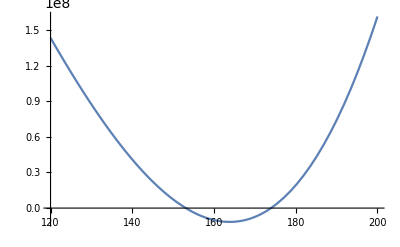

```mathematica
Plot[{exprplotmeta},{T,120,200}]
```

# Counter Term Potential (Z2 symmetric case)

```mathematica
VCT[Gp_,Gm_,G0_,h_,s_]:=ComplexExpand[-δμh Φc.Φ+ δμs/2 S^2+δλ(Φc.Φ)^2+δλs S^4/4+δλmix S^2/2 Φc.Φ+δV0]/.{ϕp->Gp,ϕm->Gm,ϕ1->h/√2,ϕ2->G0/√2,S->s};
```

```mathematica
Clear[eq1,eq2,eq3,eq4,eq5];
eq1=D[VCT[0,0,0,h,s]+V[h,s],{h,1}]/.{h->v,s->w};
eq2=D[VCT[0,0,0,h,s]+V[h,s],{s,1}]/.{h->v,s->w};
eq3=D[VCT[0,0,0,h,s]+V[h,s],{h,2}]/.{h->v,s->w};
eq4=D[VCT[0,0,0,h,s]+V[h,s],{s,2}]/.{h->v,s->w};eq5=D[D[VCT[0,0,0,h,s]+V[h,s],h],s]/.{h->v,s->w};
```

```mathematica
Solve[{eq1==0,eq2==0,eq3==0,eq4==0,eq5==0},{δμh,δμs,δλmix,δλs,δλ}]
```

{{δμh→-(-3 V^(1,0)[v,w]+w V^(1,1)[v,w]+v V^(2,0)[v,w])/(2 v),δμs→-(3 V^(0,1)[v,w]-w V^(0,2)[v,w]-v V^(1,1)[v,w])/(2 w),δλmix→-(V^(1,1)[v,w])/(v w),δλs→-(-V^(0,1)[v,w]+w V^(0,2)[v,w])/(2 w^3),δλ→-(-V^(1,0)[v,w]+v V^(2,0)[v,w])/(2 v^3)}}

# Profile and singlet action

```mathematica
s[z_]:=(sh-sl)/2Tanh[z/Ls-δs]+(sh+sl)/2
```

```mathematica
Limit[Integrate[FullSimplify[D[s[z],{z,2}]s[z]],z]/2,z->-Infinity]-Limit[Integrate[FullSimplify[D[s[z],{z,2}]s[z]],z]/2,z->Infinity]
```

ConditionalExpression[((sh-sl) (5 sh+sl))/(24 Ls)-((sh-sl) (sh+5 sl))/(24 Ls),(sh-sl|δs|sh+sl)∈ℝ&&Ls>0]

```mathematica
Limit[FullSimplify[D[s[z],{z,1}]s[z]],z->Infinity]-Limit[FullSimplify[D[s[z],{z,1}]s[z]],z->-Infinity]
```

ConditionalExpression[0,(sh-sl|δs|sh|sl)∈ℝ&&Ls>0]

```mathematica
FullSimplify[((sh-sl) (5 sh+sl))/(24 Ls)-((sh-sl) (sh+5 sl))/(24 Ls)]
```

(sh-sl)^2/(6 Ls)

```mathematica
D[s[z],{Ls,2}]
```

1/2 (sh-sl) ((2 z Sech[z/Ls-δs]^2)/Ls^3-(2 z^2 Sech[z/Ls-δs]^2 Tanh[z/Ls-δs])/Ls^4)

```mathematica
D[s[z],{δs,2}]
```

-(sh-sl) Sech[z/Ls-δs]^2 Tanh[z/Ls-δs]

```mathematica
D[s[z],{δs,1},{Ls,1}]
```

-((sh-sl) z Sech[z/Ls-δs]^2 Tanh[z/Ls-δs])/Ls^2

```mathematica
D[s[z],{Ls,1},{δs,1}]
```

-((sh-sl) z Sech[z/Ls-δs]^2 Tanh[z/Ls-δs])/Ls^2

# Numerical example

```mathematica
{mh,v,ms,w,α}={125,246,100,120,0.1};
ExpandAll[V0[0,0,0,h,s]]
```

(0.+0. ⅈ)-3960.38 h^2+0.0321587 h^4-2800.38 s^2+0.00473202 h^2 s^2+0.0872922 s^4+30 s^2 μ3-(s^3 μ3)/3+(s^4 μ3)/960-30. h^2 μϕs+1/2 h^2 s μϕs-63.0375 s^2 μϕs-0.00208333 h^2 s^2 μϕs+(1681 s^4 μϕs)/768000

# Potential (Kozaczuk’s case 1506.04741 )

```mathematica
ClearAll["Global`*"]
```

```mathematica
Φc={ϕp,ϕ1-I ϕ2};Φ={ϕm,ϕ1+I ϕ2};
V0[Gp_,Gm_,G0_,h_,s_]:=ComplexExpand[-μh Φc.Φ+λ(Φc.Φ)^2- μs/2 S^2-μ3 S^3/3+
λs S^4/4+λmix S^2/2 Φc.Φ+μϕs (Φc.Φ) S]/.{ϕp->Gp,ϕm->Gm,ϕ1->h/√2,ϕ2->G0/√2,S->s};
DV0[i_]:=D[V0[Gp,Gm,G0,h,s],{h,s,Gp,Gm,G0}[[i]]];MinimaConditions=Expand[Table[DV0[i],{i,1,5}]/.{Gp->0,Gm->0,G0->0,h->v,s->w}];MassMatrix[i_,j_]:=D[V0[Gp,Gm,G0,h,s],{h,s,Gp,Gm,G0}[[i]],{h,s,Gp,Gm,G0}[[j]]]/.{Gp->0,Gm->0,G0->0};
```

```mathematica
FullSimplify[MatrixForm[Table[MassMatrix[i,j],{i,1,5},{j,1,5}]]]
```

(3 h^2 λ+(s^2 λmix)/2-μh+s μϕs | h (s λmix+μϕs) | 0 | 0 | 0
h (s λmix+μϕs) | (h^2 λmix)/2+3 s^2 λs-2 s μ3-μs | 0 | 0 | 0
0 | 0 | 0 | h^2 λ+(s^2 λmix)/2-μh+s μϕs | 0
0 | 0 | h^2 λ+(s^2 λmix)/2-μh+s μϕs | 0 | 0
0 | 0 | 0 | 0 | h^2 λ+(s^2 λmix)/2-μh+s μϕs)

```mathematica
MinimaConditions
```

{v^3 λ+1/2 v w^2 λmix-v μh+v w μϕs,1/2 v^2 w λmix+w^3 λs-w^2 μ3-w μs+(v^2 μϕs)/2,0,0,0}

```mathematica
Clear[μh];μh=μh/.Solve[MinimaConditions[[1]]==0,μh][[1]]
```

1/2 (2 v^2 λ+w^2 λmix+2 w μϕs)

```mathematica
Clear[μs];μs=μs/.Solve[MinimaConditions[[2]]==0,μs][[1]]
```

(v^2 w λmix+2 w^3 λs-2 w^2 μ3+v^2 μϕs)/(2 w)

```mathematica
ExpandAll[μh]
```

v^2 λ+(w^2 λmix)/2+w μϕs

```mathematica
FullSimplify[MinimaConditions]
```

{0,0,0,0,0}

```mathematica
MassMat=Table[MassMatrix[i,j],{i,1,2},{j,1,2}]/.{h->v,s->w};MatrixForm[MassMat]
```

(2 v^2 λ | 0
0 | (v^2 λmix)/2+2 w^2 λs-w μ3)

```mathematica
ExpandAll[μs]
```

w^2 λs-w μ3

```mathematica
μϕs=-w λmix;
```